```mathematica
V[u_]:=A/2 u+(B u^σ)/((1+σ)(1+C1 u^(σ-1)))
```

```mathematica
V[u]//Simplify
```

1/2 u (A+(2 B u^σ)/((u+C1 u^σ) (1+σ)))

```mathematica
V'[u]//Simplify
```

A/2+(B u^σ (C1 u^σ+u σ))/((u+C1 u^σ)^2 (1+σ))

```mathematica
V''[u]//Simplify
```

-(B u^σ (-1+σ) (C1 u^σ (-2+σ)-u σ))/((u+C1 u^σ)^3 (1+σ))

```mathematica
J[F_]=(#^2(2#^(-1/3)/3+V'[#]+((2^(2/3)-1)(2#^(-1/3)/3-F'[#])+Subscript[S, 0] F'[#]/Subscript[e, n])))&;
```

```mathematica
J[#&][u]//Simplify
```

u^2 (A/2+(-1+2^(2/3)) (-1+2/(3 u^(1/3)))+2/(3 u^(1/3))-(B C1 u^(2 σ) (-1+σ))/((u+C1 u^σ)^2 (1+σ))+(B u^σ σ)/((u+C1 u^σ) (1+σ))+S_0/e_n)

```mathematica
J[#&]'[u]//Simplify
```

1/(9 (u+C1 u^σ)^3 (1+σ))(18 B C1^2 u^(1+3 σ)-36 B C1^2 u^(1+3 σ) σ+27 B C1 u^(1+2 σ) (u+C1 u^σ) σ+9 B u^(1+σ) (u+C1 u^σ)^2 σ+18 B C1^2 u^(1+3 σ) σ^2-27 B C1 u^(1+2 σ) (u+C1 u^σ) σ^2+9 B u^(1+σ) (u+C1 u^σ)^2 σ^2+10 2^(2/3) u^(2/3) (u+C1 u^σ)^3 (1+σ)+18 u (u+C1 u^σ)^3 (1+σ)-18 2^(2/3) u (u+C1 u^σ)^3 (1+σ)+9 A u (u+C1 u^σ)^3 (1+σ))+(2 u S_0)/e_n

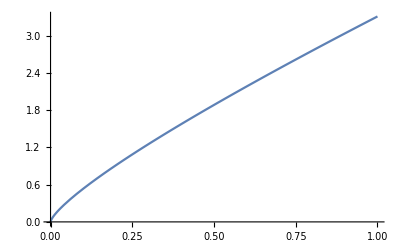

```mathematica
Plot[((J[#&]'[u])/.{Subscript[e, n]->3.53714255054277746402*10^-12,F[u]->u,Subscript[S, 0]->4.80652985999999999982*10^-12,A->-30.0191740681034304802*3.53714255054277746402*10^-12,B->30.4279212752455208695*3.53714255054277746402*10^-12,C1->0.2,σ->1.12616484949237465702}),{u,0,1}]
```

```mathematica
En[u_,α_]:=m c^2+Subscript[e, n] u^(2/3)+V[u]+α^2(Subscript[e, n](2^(2/3)-1)(u^(2/3)-F[u])+Subscript[S, 0] F[u])
```

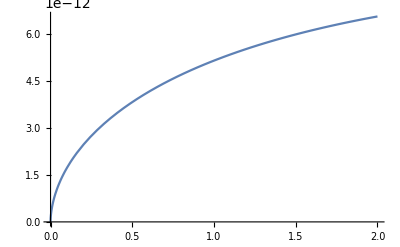

```mathematica
Plot[(En[u,1]-m c^2)/.{Subscript[e, n]->3.53714255054277746402*10^-12,F[u]->Sqrt[u],Subscript[S, 0]->4.80652985999999999982*10^-12,A->0.90563*3.53714255054277746402*10^-12,B->-3.19611*3.53714255054277746402*10^-12,C1->0.2,σ->0.969846},{u,0,2}]
```

```mathematica
D[En[u,0],u]/.{u->1}//Simplify
```

A/2+(B (C1+σ))/((1+C1)^2 (1+σ))+(2 e_n)/3

```mathematica
(*Solve[{(D[En[u,1],u]/.{u->1})==0,En[1,1]-m c^2==Eb,(D[En[u,1],{u,2}]/.{u->1})==K0}/.{F[1]->1},{A,B,σ}]//Simplify;*)
```

```mathematica
Asol=First[Solve[(D[En[u,0],u]/.{u->1})==0,A]//Simplify]
```

{A→-(2 B (C1+σ))/((1+C1)^2 (1+σ))-(4 e_n)/3}

```mathematica
Bsol=First[Solve[(En[1,0]/.Asol)-m c^2==Eb,B]//Simplify]
```

{B→-((1+C1)^2 (1+σ) (3 Eb-e_n))/(3 (-1+σ))}

```mathematica
σsol=First[Solve[(((D[En[u,0],{u,2}]/.{u->1})/.Asol)/.Bsol)==K0,σ]//Simplify]
```

{σ→(9 (K0+C1 (2 Eb+K0))+(2-4 C1) e_n)/(3 (-1+C1) (3 Eb-e_n))}

```mathematica
(Subscript[e, n] (2 2^(2/3)+9 (-1+2^(2/3)) F''[1]+C1 (-4 2^(2/3)+18 (-1+2^(2/3)) F[1]-18 (-1+2^(2/3)) F'[1]-9 F''[1]+9 2^(2/3) F''[1]))+9 (K0+C1 (2 Eb+K0)-Subscript[S, 0] (F''[1]+C1 (2 F[1]-2 F'[1]+F''[1]))))/(3 (-1+C1) (Subscript[e, n] (-2^(2/3)+3 (-1+2^(2/3)) F[1]-3 (-1+2^(2/3)) F'[1])+3 (Eb+Subscript[S, 0] (-F[1]+F'[1]))))/.{K0->100,C1->0.1,Eb->1,F[1]->1,F'[1]->1,F''[1]->1,Subscript[e, n]->1,Subscript[S, 0]->1}
```

-259.636

```mathematica
-1/(3 (-1+σ))(1+C1)^2 (1+σ) (Subscript[e, n] (-2^(2/3)+3 (-1+2^(2/3)) F[1]-3 (-1+2^(2/3)) F'[1])+3 (Eb+Subscript[S, 0] (-F[1]+F'[1])))/.{K0->100,C1->0.1,Eb->1,F[1]->1,F'[1]->1,F''[1]->0,Subscript[e, n]->1,Subscript[S, 0]->1,σ->1.2}
```

-6.26723

```mathematica
-(2 B (C1+σ))/((1+C1)^2 (1+σ))-2 Subscript[S, 0] F'[1]+2/3 Subscript[e, n] (-2 2^(2/3)+3 (-1+2^(2/3)) F'[1])/.{K0->100,C1->0.1,Eb->1,F[1]->1,F'[1]->1,F''[1]->0,Subscript[e, n]->1,Subscript[S, 0]->1,σ->1.2,B->1.4}
```

-4.30913

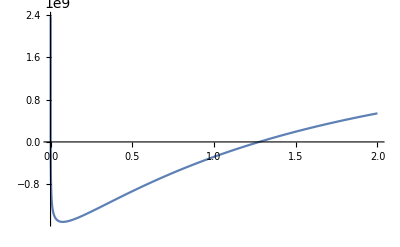

```mathematica
Plot[(D[e0*((3/10)v^(2/3)+V[v]),v]/.{v->u})/.{e0->1.50431*10^-10/(1.6*10^-19),A->-4.46737,B->3.78879,σ->2.088,C1->0.3},{u,0,2}]
```

```mathematica
(σ/.σsol)/.{Subscript[e, n]->5.61486*10^-12,K0->3.11534*10^-12,Eb->-2.56348*10^-12,C1->0.3}
```

0.969845

```mathematica
(B/.Bsol)/Subscript[e, n]/.{Subscript[e, n]->5.61486*10^-12,K0->3.11534*10^-12,Eb->-2.56348*10^-12,C1->0.3,σ->0.9698453140585225}
```

-87.2024

```mathematica
(A/.Asol)/.{Subscript[e, n]->5.61486*10^-12,K0->3.11534*10^-12,Eb->-2.56348*10^-12,C1->0.3,σ->0.9698453140585225,B->-87.2024130843038}
```

66.5259

```mathematica
Solve[(D[En[u,0],u]/.{u->1})==0,σ]//Simplify
```

{{σ→(-3 (2 B C1+A (1+C1)^2)-4 (1+C1)^2 e_n)/(3 (2 B+A (1+C1)^2)+4 (1+C1)^2 e_n)}}

```mathematica
Solve[(En[1,0]/.{σ->(-3 (2 B C1+A (1+C1)^2)-4 (1+C1)^2 Subscript[e, n])/(3 (2 B+A (1+C1)^2)+4 (1+C1)^2 Subscript[e, n])})-m c^2==Eb,B]//Simplify
```

{{B→-1/3 (1+C1) (3 (A+(-1+C1) Eb)-(-5+C1) e_n)}}

```mathematica
Solve[((D[En[u,0],{u,2}]/.{u->1,σ->(-3 (2 B C1+A (1+C1)^2)-4 (1+C1)^2 Subscript[e, n])/(3 (2 B+A (1+C1)^2)+4 (1+C1)^2 Subscript[e, n])})/.{B->-1/3 (1+C1) (3 (A+(-1+C1) Eb)-(-5+C1) Subscript[e, n])})==K0,A]//Simplify
```

{{A→(2 (9 Eb (C1 Eb+K0)-((4+6 C1) Eb+9 K0) e_n+C1 e_n^2))/(9 (Eb+K0)-e_n)}}

```mathematica
(2 (9 Eb (C1 Eb+K0)-((4+6 C1) Eb+9 K0) Subscript[e, n]+C1 Subscript[e, n]^2))/(9 (Eb+K0)-Subscript[e, n])/Subscript[e, n]/.{Subscript[e, n]->5.61486*10^-12,K0->3.11534*10^-12,Eb->-2.56348*10^-12,C1->0.3}
```

65.1925

```mathematica
D[1/(1+C1 u^(σ-1)),u]//Simplify
```

-(C1 u^σ (-1+σ))/((u+C1 u^σ)^2)